```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
RinfC[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - -I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[I k r]Hypergeometric1F1[-I/(k a0)+l+1,2l+2,- 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
Integrate[Rb[2,1,r]^2 r^2,{r,0,Infinity}]
```

ConditionalExpression[1, Re[a0]>0]

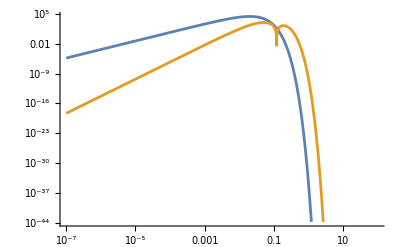

```mathematica
LogLogPlot[{Rb[2,1,r]^2/.{a0-> 0.01},Rb[4,2,r]^2/.{a0-> 0.01}},{r,10^-7,100}]
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
Solve[α== GM μ,GM]
```

{{GM→α/μ}}

```mathematica
temp=N[FullSimplify[Solve[ωerg[2,α,μ]== m a/(2 (α/μ) (1+√(1-a^2)))/.{a->0.998},α]]/.{m-> 1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-2.58296},{α→0.483683},{α→2.19829},{α→-0.0495058-4.6767 ⅈ},{α→-0.0495058+4.6767 ⅈ}}

```mathematica
temp=N[FullSimplify[Solve[ωerg[3,α,μ]== m a/(2 (α/μ) (1+√(1-a^2)))/.{a->0.998},α]]/.{m-> 2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-3.94448},{α→0.994873},{α→3.14737},{α→-0.0988806-7.01692 ⅈ},{α→-0.0988806+7.01692 ⅈ}}

## 322 x 322 → 211 x Inf

```mathematica
(*322 x 322 -> 211 x Inf*)
```

```mathematica
α(2(1-α^2/(2 3^2))- (1-α^2/(2 2^2)))/.{α->0.03143351069,n->2}
```

0.0314339

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c) ;
```

```mathematica
Coefficient[1/6 Expand[ϕ1^3], ⅇ^(-2 ⅈ t ω3-ⅈ t ω2)]
```

1/2 α2 α3^2 ψ2 ψ3^2

```mathematica
FullSimplify[Conjugate[SphericalHarmonicY[1,1,θ,ϕ]]SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,2,θ,ϕ]Conjugate[SphericalHarmonicY[3,3,θ,ϕ]],θ∈Reals&&ϕ∈Reals]
```

(15 √(105/2) Sin[θ]^8)/(512 π^2)

```mathematica
CG = Block[{l=3,m=-3},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

-(√(5/42))/π

```mathematica
N[((√(5/42))/π)]
```

0.109827

```mathematica
SphericalHarmonicY[2,2,1.1,1.1]
```

-0.180551+0.248045 ⅈ

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
ωnew = 2 ωerg[3,α,μ]-ωerg[2,α,μ]//FullSimplify
```

μ+(α^2 μ)/72

```mathematica
k=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]]
```

(α μ)/6

```mathematica
(*rr = r (α μ)
r^2 dr = (rr^2 drr)/(α μ)^3*)
```

```mathematica
FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]
```

(r^2 (r/(α μ))'[x])/(α^2 μ^2)

```mathematica
holdT = 1/(α^(11/2) μ^4)FullSimplify[1/2 1/(2μ)^(3/2)Conjugate[Rinf[k,3,r ]] Rb[3,2,r]^2 Rb[2,1,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

(ⅇ^(3 π-(7/6-ⅈ/6) r) r^8 Abs[Gamma[4-6 ⅈ]] Conjugate[Hypergeometric1F1[4+6 ⅈ,8,(ⅈ r)/3]])/(80353879200 √3)

```mathematica
ff=FullSimplify[(CG (4π)(-I)^l)/(2 k)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity}]/.{l->3},α>0&&μ>0&&r∈Reals]
```

(0.-0.00231833 ⅈ) α^(3/2)

```mathematica
fac=Normal[Series[ωnew k,{α,0,1}]]
```

(α μ^2)/6

```mathematica
FullSimplify[Series[2  (fac)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.13451×10^-8 λ^2 μ^2 α^4+O[α]^6

```mathematica
1.1345106363755355*^-8 λ^2 μ^2 α^4/.{λ->1,μ->2 3 10^-13,α->2 0.0314}
```

6.35257×10^-38

```mathematica
1.1345106363755355*^-8 λ^2 μ^2 α^4/.{λ->1,μ-> 3 10^-13,α-> 0.0314}
```

9.92589×10^-40

```mathematica
6.352572754125904*^-38 / 9.925894928321725*^-40
```

64.

## 422 x 322 → 211 x Inf [compute!!]

```mathematica
(*322 x 322 -> 211 x Inf*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 +α4 Exp[-I ω4 t]ψ4+ α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c +α4 Exp[I ω4 t]ψ4c) ;
```

```mathematica
Coefficient[1/6 Expand[ϕ1^3], ⅇ^(-( ω3 ⅈ t  + ω4 ⅈ t - ω2 ⅈ t ))]
```

α2 α3 α4 ψ2c ψ3 ψ4

```mathematica
CG = Block[{l=3,m=-3},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

-(√(5/42))/π

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
ωnew =  ωerg[4,α,μ]+ωerg[3,α,μ]-ωerg[2,α,μ]//FullSimplify
```

μ+(11 α^2 μ)/288

```mathematica
k=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]]
```

1/12 √11 α μ

```mathematica
FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]
```

(r^2 (r/(α μ))'[x])/(α^2 μ^2)

```mathematica
fullIn =1/(α^(11/2) μ^4)FullSimplify[1/(2μ)^(3/2)RinfC[k,3,r ]Rb[4,2,r]Rb[3,2,r]Rb[2,1,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

-(121 ⅇ^((6 π)/(√11)+1/12 ⅈ (13 ⅈ+√11) r) (-12+r) r^8 Abs[Gamma[4+(12 ⅈ)/(√11)]] Hypergeometric1F1[4-(12 ⅈ)/(√11),8,-1/6 ⅈ √11 r])/(12189981081600 √2)

```mathematica
ff=FullSimplify[(CG (4π)(-I)^l)/(2 k)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[fullIn r^2,{r,0,Infinity},Method->"AdaptiveQuasiMonteCarlo"]/.{l->3},α>0&&μ>0&&r∈Reals]
```

(0.-0.00215088 ⅈ) α^(3/2)

```mathematica
fac=Normal[Series[ωnew k,{α,0,1}]]
```

1/12 √11 α μ^2

```mathematica
FullSimplify[Series[ 2 (fac)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.61941×10^-8 λ^2 μ^2 α^4+O[α]^6

```mathematica
1.619411939436326*^-8 λ^2 μ^2 α^4/.{λ->1,μ-> 5 10^-12,α-> 0.52389184}
```

3.04975×10^-32

## 411 x 322 → 211 x Inf [compute!!]

```mathematica
(*322 x 322 -> 211 x Inf*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(√(N211/(2 μ)) Exp[-I ω2 t]ψ2 + √(N322/(2 μ)) Exp[-I ω3 t]ψ3 +√(N411/(2 μ)) Exp[-I ω4 t]ψ4 +√(N211/(2 μ))  Exp[I ω2 t]ψ2c +√(N322/(2 μ))  Exp[I ω3 t]ψ3c+√(N411/(2 μ)) Exp[I ω4 t]ψ4 ) ;
ϕ1c=(√(N211/(2 μ)) Exp[I ω2 t]ψ2 + √(N322/(2 μ)) Exp[I ω3 t]ψ3 +√(N211/(2 μ))  Exp[-I ω2 t]ψ2c +√(N322/(2 μ))  Exp[-I ω3 t]ψ3c) ;
```

```mathematica
FullSimplify[Expand[ϕ1^2 /. {ψ2 ψ2c-> 1, ψ3 ψ3c-> 1}]]
```

1/(2 μ)(ⅇ^(-2 ⅈ t ω2) N211 ψ2^2+2 N211 ψ2 ψ2c+ⅇ^(2 ⅈ t ω2) N211 ψ2c^2+2 ⅇ^(-ⅈ t (ω2+ω3)) √(N211/μ) √(N322/μ) μ ψ2 ψ3+2 ⅇ^(ⅈ t (ω2-ω3)) √(N211/μ) √(N322/μ) μ ψ2c ψ3+ⅇ^(-2 ⅈ t ω3) N322 ψ3^2+2 ⅇ^(-ⅈ t (ω2-ω3)) √(N211/μ) √(N322/μ) μ ψ2 ψ3c+2 ⅇ^(ⅈ t (ω2+ω3)) √(N211/μ) √(N322/μ) μ ψ2c ψ3c+2 N322 ψ3 ψ3c+ⅇ^(2 ⅈ t ω3) N322 ψ3c^2)

```mathematica
Coefficient[1/6 Expand[ϕ1^3], ⅇ^(-2 ⅈ t ω3+ⅈ t ω2)]
```

(N322 √(N211/μ) ψ2c ψ3^2)/(4 √2 μ)

```mathematica
Coefficient[1/6 Expand[ϕ1^3], ⅇ^(-( ⅈ t ω3+ⅈ t ω4-ⅈ t ω2))]
```

(√(N211/μ) √(N322/μ) √(N411/μ) ψ2c ψ3 ψ4)/(2 √2)

```mathematica
CG = Block[{l=2,m=-2},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[2,2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

9/(28 π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
ωnew =  ωerg[4,α,μ]+ωerg[3,α,μ]-ωerg[2,α,μ]//FullSimplify
```

μ+(11 α^2 μ)/288

```mathematica
k=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]]
```

1/12 √11 α μ

```mathematica
(*FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]

(r^2 (r/(α μ))'[x])/(α^2 μ^2)*)
```

```mathematica
holdIn = FullSimplify[1/((α)^(11/2) μ^4)1/(2μ)^(3/2)RinfC[k,2,r ]Rb[4,1,r]Rb[3,2,r]Rb[2,1,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

(11 √(11/6) ⅇ^((6 π)/(√11)+1/12 ⅈ (13 ⅈ+√11) r) r^6 (80+(-20+r) r) Abs[Gamma[3+(12 ⅈ)/(√11)]] Hypergeometric1F1[3-(12 ⅈ)/(√11),6,-1/6 ⅈ √11 r])/16124313600

```mathematica
(*ff=FullSimplify[(CG (4π)(-I)^l)/(2 k)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdIn r^2,{r,0,Infinity}]/.{l->3},α>0&&μ>0&&r∈Reals]*)
```

```mathematica
ff=FullSimplify[(CG (4π)(-I)^l)/(2 k)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdIn r^2,{r,0,Infinity},Method->"AdaptiveQuasiMonteCarlo"]/.{l->3},α>0&&μ>0&&r∈Reals]
```

(0.+0.001033 ⅈ) α^(3/2)

```mathematica
fac=Normal[Series[ωnew k,{α,0,1}]]
```

1/12 √11 α μ^2

```mathematica
FullSimplify[Series[ 2 (fac)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.73532×10^-9 λ^2 μ^2 α^4+O[α]^6

## 211 x 211 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c) ;
```

```mathematica
Coefficient[Expand[ϕ1^3], ⅇ^(-2 ⅈ t ω3-ⅈ t ω2)]
```

3 α2 α3^2 ψ2 ψ3^2

```mathematica
FullSimplify[SphericalHarmonicY[2,-2,θ,ϕ](-1)^2 SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]]
```

(3 √(15/2) Sin[θ]^4)/(32 π^(3/2))

```mathematica
ωnew =  ωerg[2,α,μ]+ωerg[2,α,μ]-ωerg[3,α,μ]//FullSimplify
```

μ-(7 α^2 μ)/36

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- (ωnew)^2,{α,0,2}]]]
```

(7 α^2 μ^2)/18

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
```

1/(2 √π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
RinfC[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - -I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[I k r]Hypergeometric1F1[-I/(k a0)+l+1,2l+2,- 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]
```

(r^2 (r/(α μ))'[x])/(α^2 μ^2)

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
Limit[Rb[1,0,r],r->0]
```

2 √(1/a0^3)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[2,1,r/(α μ)]Rb[3,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
 SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)};
,{n,1,10}]);
```

```mathematica
val
```

-(0.0000845057 α √(α^3 μ^3))/(√μ)

```mathematica
FullSimplify[1/μ 4 α^2 λ^2 val^2,α>0&&μ>0]
```

2.85649×10^-8 α^7 λ^2 μ

```mathematica
(*k > 0 part*)
```

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[2,1,r/(α μ)]Rb[3,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
Abs[ SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)}];
,{n,1,20}]);
```

```mathematica
intTerm= FullSimplify[1/(2π)1/(k2+(kk α μ)^2)1/2 1/(2μ)^(3/2)RinfC[kk α μ ,0,r]Rb[2,1,r] Rb[2,1,r]Rb[3,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)} ,α>0&&μ>0]
```

(ⅇ^(π/(2 kk)-(4 r)/3+ⅈ kk r) kk r^4 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(216 √15 (7+18 kk^2) π)

```mathematica
intV=Table[{kk,Abs[NIntegrate[1/(α^(7/2) μ^2)intTerm r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->5]]},{kk,0.01,2,.01}];
```

```mathematica
N[(7/18)]
```

0.388889

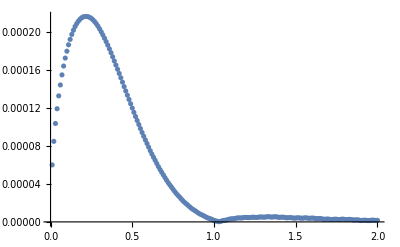

```mathematica
ListPlot[intV]
```

```mathematica
intVInter=Interpolation[Re[intV]];
```

```mathematica
rad0=Limit[Rinf[kk α μ,0,r]/.{ a0-> 1/(μ α)},r->0]
```

2 ⅇ^(π/(2 kk)) kk α μ Abs[Gamma[1-ⅈ/kk]]

```mathematica
(*alpha terms [factored out of radial integral, jacobian r, jacobian k, k2 term, rad0 term]]*)
```

```mathematica
val+= FullSimplify[SphericalHarmonicY[0,0,θ,ϕ] 1/μ^(3/2)(α μ)^(7/2)  (1/(α μ))^3 (α μ)α μ NIntegrate[intVInter[kk] rad0/(α μ),{kk,0.001,2.2}],α>0&&μ>0&&r∈Reals]
```

0.000189176 α^(5/2) μ+0.0000847612 Abs[(α √(α^3 μ^3))/(√μ)]

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.00167×10^-7 λ^2 μ α^7+O[α]^(19/2)

```mathematica
t1=4.3 10^-7 μ  α^11(1+√(1-a^2))/.{λ-> 1, μ-> 3 10^-13, α->0.0314334,a->0.9}
```

5.48297×10^-36

```mathematica
t2=4.3 10^-7  μ α^11(1+√(1-a^2))/.{λ-> 1, μ->2  3 10^-13, α->2 0.0314334,a->0.9}
```

2.24582×10^-32

```mathematica
(t2/t1)
```

4096.

```mathematica
2^12
```

4096

## 211 x 211 → 422 x BH

```mathematica
(*211 x 211 -> 422 x BH*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c) ;
```

```mathematica
Coefficient[Expand[ϕ1^3], ⅇ^(-2 ⅈ t ω3-ⅈ t ω2)]
```

3 α2 α3^2 ψ2 ψ3^2

```mathematica
FullSimplify[SphericalHarmonicY[2,-2,θ,ϕ](-1)^2 SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]]
```

(3 √(15/2) Sin[θ]^4)/(32 π^(3/2))

```mathematica
ωnew =  ωerg[2,α,μ]+ωerg[2,α,μ]-ωerg[4,α,μ]//FullSimplify
```

μ-(7 α^2 μ)/32

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,2}]]]
```

(7 α^2 μ^2)/16

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
```

1/(2 √π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]
```

(r^2 (r/(α μ))'[x])/(α^2 μ^2)

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[2,1,r/(α μ)]Rb[4,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
Abs[ SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)}];
,{n,1,50}]);
```

```mathematica
4π FullSimplify[1/μ 4 α^2 λ^2 val^2,α>0&&μ>0]
```

1.25403×10^-7 α^7 λ^2 μ

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Rb[1,0,r ]Rb[2,1,r] Rb[2,1,r]Rb[4,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

-(ⅇ^(-9 r/4) (-12+r) r^4 α^6 μ^(9/2))/(36864 √10)

```mathematica
ff1=FullSimplify[CG/(k2-(α^2 μ^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[-(ⅇ^(-9 r/4) (-12+r) r^4)/(36864 √10) r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals]
```

-(0.0000291446 α)/(√μ)

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Rb[2,0,r ]Rb[2,1,r] Rb[2,1,r]Rb[4,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

(ⅇ^(-7 r/4) (-12+r) (-2+r) r^4 α^6 μ^(9/2))/(294912 √5)

```mathematica
ff2=FullSimplify[CG/(k2-((α^2 μ^2)/2^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[(ⅇ^(-7 r/4) (-12+r) (-2+r) r^4)/(294912 √5) r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals]
```

-(0.000138497 α)/(√μ)

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Rb[3,0,r ]Rb[2,1,r] Rb[2,1,r]Rb[4,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

-(ⅇ^(-19 r/12) (-12+r) r^4 (27+2 (-9+r) r) α^6 μ^(9/2))/(2985984 √30)

```mathematica
ff3=FullSimplify[CG/(k2-((α^2 μ^2)/3^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[-(ⅇ^(-19 r/12) (-12+r) r^4 (27+2 (-9+r) r))/(2985984 √30) r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals]
```

-(0.0000311402 α)/(√μ)

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Rb[4,0,r ]Rb[2,1,r] Rb[2,1,r]Rb[4,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

(ⅇ^(-3 r/2) (-12+r) r^4 (-192+(-12+r)^2 r) α^6 μ^(9/2))/(56623104 √10)

```mathematica
ff4=FullSimplify[CG/(k2-((α^2 μ^2)/4^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[(ⅇ^(-3 r/2) (-12+r) r^4 (-192+(-12+r)^2 r))/(56623104 √10) r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals]
```

-(0.0000155613 α)/(√μ)

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Rb[5,0,r ]Rb[2,1,r] Rb[2,1,r]Rb[4,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

-(ⅇ^(-29 r/20) (-12+r) r^4 (9375+2 r (-3750+r (750+(-50+r) r))) α^6 μ^(9/2))/(8640000000 √2)

```mathematica
ff5=FullSimplify[CG/(k2-((α^2 μ^2)/5^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[-(ⅇ^(-29 r/20) (-12+r) r^4 (9375+2 r (-3750+r (750+(-50+r) r))))/(8640000000 √2) r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals]
```

-(9.91146×10^-6 α)/(√μ)

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]^2
```

1/(4 π)

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 SphericalHarmonicY[0,0,θ,ϕ]^2(Normal[Series[Rb[1,0,r],{r,0,0}]]ff1+Normal[Series[Rb[2,0,r],{r,0,0}]]ff2+Normal[Series[Rb[3,0,r],{r,0,0}]]ff3+Normal[Series[Rb[4,0,r],{r,0,0}]]ff4+Normal[Series[Rb[5,0,r],{r,0,0}]]ff5)^2/.{a0->(μ α)^-1},{α,0,7}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

9.62285×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(4.3 10^-7)/(9.2 10^-9)
```

46.7391

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (ff1+ff2+ff3+ff4+ff5)^2/.{a0->(μ α)^-1},{α,0,7}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

(2.01161×10^-7 λ^2 α^4)/μ^2+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Conjugate[Rinf[kk α μ,0,r]]Rb[2,1,r] Rb[2,1,r]Rb[4,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&kk∈Reals&&α∈Reals&&μ∈Reals&&r∈Reals]
```

-(ⅇ^(π/(2 kk)-(5 r)/4+ⅈ kk r) kk (-12+r) r^4 α^(11/2) μ^4 Abs[Gamma[(-ⅈ+kk)/kk]] Conjugate[Hypergeometric1F1[(ⅈ+kk)/kk,2,2 ⅈ kk r]])/(36864 √10)

```mathematica
intV=Table[{kk,Abs[NIntegrate[1/(2π)CG 1/((k2 /(α^2 μ^2)) +kk^2)(-(ⅇ^(π/(2 kk)-(5 r)/4+ⅈ kk r) kk (-12+r) r^4  Abs[Gamma[(-ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(36864 √10) r^2),{r,0,Infinity}]]},{kk,0.01,2,.005}];
```

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.69191}. NIntegrate obtained -2.7168×10^-6-1.99051×10^-20 ⅈ and 3.07883×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.68119}. NIntegrate obtained -2.56239×10^-6+3.69571×10^-20 ⅈ and 4.76537×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.5461}. NIntegrate obtained -1.93566×10^-6-5.57107×10^-20 ⅈ and 2.14634×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::inumr: The integrand -(ⅇ^(π/(2 kk)-(5 r)/4+ⅈ kk r) kk (-12+r) r^6 Abs[Gamma[(-ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(491520 √3 (7/16+kk^2) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
intVInter=Interpolation[Re[intV]];
```

NIntegrate::inumr: The integrand -(ⅇ^(π/(2 kk)-(5 r)/4+ⅈ kk r) kk (-12+r) r^6 Abs[Gamma[(-ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(491520 √3 (7/16+kk^2) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
ListPlot[intV]
```

NIntegrate::inumr: The integrand -(ⅇ^(π/(2 kk)-(5 r)/4+ⅈ kk r) kk (-12+r) r^6 Abs[Gamma[(-ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(491520 √3 (7/16+kk^2) π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
Normal[Series[Rinf[kk α μ,0,r]/.{ a0-> 1/(μ α)},{r,0,0}]]
```

2 ⅇ^(π/(2 kk)) kk α μ Abs[Gamma[1-ⅈ/kk]]

```mathematica
val=FullSimplify[α^(11/2) μ^4 (1/(α μ))^3 1/(α μ)1/(α μ)^-2 NIntegrate[intVInter[kk] 2 ⅇ^(π/(2 kk)) kk Abs[Gamma[1-ⅈ/kk]],{kk,0.001,2}],α>0&&μ>0&&r∈Reals]
```

53977. α^(7/2) μ^2

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.6394×10^8 λ^2 μ^3 α^9+O[α]^10

## 411 x 422 → 211 x Inf

```mathematica
(*411 x 422 -> 211 x Inf*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c) ;
```

```mathematica
Coefficient[Expand[ϕ1^3], ⅇ^(-2 ⅈ t ω3-ⅈ t ω2)]
```

3 α2 α3^2 ψ2 ψ3^2

```mathematica
FullSimplify[SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]]
```

(3 √(15/2) ⅇ^(2 ⅈ ϕ) Sin[θ]^4)/(32 π^(3/2))

```mathematica
CG = Block[{l=2,m=-2},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

9/(28 π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
ωnew =  ωerg[4,α,μ]+ωerg[4,α,μ]-ωerg[2,α,μ]//FullSimplify
```

μ+(α^2 μ)/16

```mathematica
k=Normal[FullSimplify[Series[√(ωnew^2-μ^2),{α,0,2}],μ>0&&α>0]]
```

(α μ)/(2 √2)

```mathematica
FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]
```

(r^2 (r/(α μ))'[x])/(α^2 μ^2)

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Conjugate[Rinf[k,2,r ]]Rb[4,2,r] Rb[4,1,r]Rb[2,1,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

-(ⅇ^(√2 π+1/4 ⅈ (4 ⅈ+√2) r) (-12+r) r^6 (80+(-20+r) r) α^(11/2) μ^4 Abs[Gamma[3-2 ⅈ √2]] Conjugate[Hypergeometric1F1[3+2 ⅈ √2,6,(ⅈ r)/(√2)]])/(11324620800 √2)

```mathematica
ff=FullSimplify[(CG (4π)(-I)^l)/(2 k)α^(11/2) μ^4(1/(α μ))^3 NIntegrate[-(ⅇ^(√2 π+1/4 ⅈ (4 ⅈ+√2) r) (-12+r) r^6 (80+(-20+r) r)  Abs[Gamma[3-2 ⅈ √2]] Hypergeometric1F1[3-2 ⅈ √2,6,(-ⅈ r)/(√2)])/(11324620800 √2),{r,0,Infinity}]/.{l->3},α>0&&μ>0&&r∈Reals]
```

(4.84386×10^-13+0.0000343329 ⅈ) α^(3/2)

```mathematica
Series[ωnew k,{α,0,1}]
```

(μ^2 α)/(2 √2)+O[α]^2

```mathematica
FullSimplify[Series[ 2 ((μ^2 α)/(2 √2))/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.27819×10^-12 λ^2 μ^2 α^4+O[α]^6

```mathematica
5.278193048805911*^-12 λ^2 μ^2 α^4/.{λ-> (μ/fa)^2}
```

(5.27819×10^-12 α^4 μ^6)/fa^4

## 411 x 411 → 422 x BH

```mathematica
(*411 x 411 -> 422 x BH*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
FullSimplify[SphericalHarmonicY[2,-2,θ,ϕ](-1)^2 SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]]
```

(3 √(15/2) Sin[θ]^4)/(32 π^(3/2))

```mathematica
ωnew =  ωerg[4,α,μ]+ωerg[4,α,μ]-ωerg[4,α,μ]//FullSimplify
```

μ-(α^2 μ)/32

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,4}]]]
```

(α^2 μ^2)/16-(α^4 μ^2)/1024

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
```

1/(2 √π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
(√(3/10))/(2 π)
```

(√(3/10))/(2 π)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[4,1,r/(α μ)] Rb[4,1,r/(α μ)]Rb[4,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
 SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)};
,{n,1,20}]);
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,3}],α>0&&μ>0]
```

1.82979×10^-8 λ^2 μ α^3+O[α]^(7/2)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[4,1,r/(α μ)] Rb[4,1,r/(α μ)]Rb[4,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
Abs[ SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)}];
,{n,1,20}]);
```

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,4}]]]
```

(α^2 μ^2)/16-(α^4 μ^2)/1024

```mathematica
intTerm= FullSimplify[1/(2π)1/((kk α μ)^2)1/2 1/(2μ)^(3/2)RinfC[kk α μ ,0,r]Rb[4,1,r] Rb[4,1,r]Rb[4,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)} ,α>0&&μ>0]
```

-(ⅇ^(π/(2 kk)-(3 r)/4+ⅈ kk r) (-12+r) r^4 (80+(-20+r) r)^2 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(3019898880 √10 kk π)

```mathematica
intV=Table[{kk,Abs[NIntegrate[1/(α^(7/2) μ^2)intTerm r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->5]]},{kk,0.1,2,.01}];
```

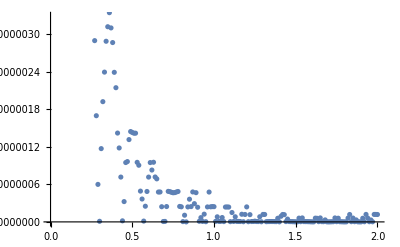

```mathematica
ListPlot[intV]
```

```mathematica
intVInter=Interpolation[Re[intV]];
```

```mathematica
rad0=Limit[Rinf[kk α μ,0,r]/.{ a0-> 1/(μ α)},r->0]
```

2 ⅇ^(π/(2 kk)) kk α μ Abs[Gamma[1-ⅈ/kk]]

```mathematica
(*alpha terms [factored out of radial integral, jacobian r, jacobian k, k2 term, rad0 term]]*)
```

```mathematica
val+= FullSimplify[SphericalHarmonicY[0,0,θ,ϕ] 1/μ^(3/2)(α μ)^(7/2)  (1/(α μ))^3 (α μ)α μ NIntegrate[intVInter[kk] rad0/(α μ),{kk,0.001,2.2}],α>0&&μ>0&&r∈Reals]
```

0.0000218876 α^(5/2) μ+0.0000676349 Abs[(√(α^3 μ^3))/(α √μ)]+8.49476×10^-7 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/(-15/16 α^2 μ^2-(α^4 μ^2)/1024)]+2.9737×10^-7 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/(-3/16 α^2 μ^2-(α^4 μ^2)/1024)]+7.74088×10^-8 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/(-7/144 α^2 μ^2-(α^4 μ^2)/1024)]+1.88909×10^-8 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((9 α^2 μ^2)/400-(α^4 μ^2)/1024)]+6.32665×10^-9 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((5 α^2 μ^2)/144-(α^4 μ^2)/1024)]+2.43602×10^-9 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((33 α^2 μ^2)/784-(α^4 μ^2)/1024)]+1.0245×10^-9 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((3 α^2 μ^2)/64-(α^4 μ^2)/1024)]+4.49067×10^-10 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((65 α^2 μ^2)/1296-(α^4 μ^2)/1024)]+1.94449×10^-10 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((21 α^2 μ^2)/400-(α^4 μ^2)/1024)]+7.54819×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((105 α^2 μ^2)/1936-(α^4 μ^2)/1024)]+1.82079×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((α^2 μ^2)/18-(α^4 μ^2)/1024)]+9.44965×10^-12 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((153 α^2 μ^2)/2704-(α^4 μ^2)/1024)]+2.23335×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((45 α^2 μ^2)/784-(α^4 μ^2)/1024)]+2.76698×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((209 α^2 μ^2)/3600-(α^4 μ^2)/1024)]+2.91184×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((15 α^2 μ^2)/256-(α^4 μ^2)/1024)]+2.85885×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((273 α^2 μ^2)/4624-(α^4 μ^2)/1024)]+2.70962×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((77 α^2 μ^2)/1296-(α^4 μ^2)/1024)]+2.51878×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((345 α^2 μ^2)/5776-(α^4 μ^2)/1024)]+2.31564×10^-11 Abs[(α^3 μ^(3/2) √(α^3 μ^3))/((3 α^2 μ^2)/50-(α^4 μ^2)/1024)]

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.82979×10^-8 λ^2 μ α^3+1.46585×10^-8 λ^2 μ α^5+2.93709×10^-9 λ^2 μ α^7+1.87192×10^-12 λ^2 μ α^9+O[α]^11

```mathematica
1.829791034806738*^-8 λ^2 μ α^3 √(1-aa^2)/.{λ->1,μ-> 3 10^-13, α->0.031433510698, aa->0.9}
```

7.43153×10^-26

```mathematica
1.829791034806738*^-8 λ^2 μ α^3 √(1-aa^2)/.{λ->1,μ-> 2 3 10^-13, α->2 0.031433510698,aa->0.9}
```

1.18904×10^-24

```mathematica
(1.1890447477776922*^-24)/(7.431529673610576*^-26)
```

16.

```mathematica
1.829791034806738*^-8   α^7/.{μ->3 10^-13,α-> 0.031 ,a->0.9}
```

5.03423×10^-19

## 211 x 411 → 322 x BH

```mathematica
ωerg2[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^4(2l-3n + 1)/(l+1/2));
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
n1=2;n2=4;n3=3;
l1=m1=1;l2=m2=1;l3=m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
(Do[hold=1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};

ωnew =  ωerg2[n1,α,μ,l1]+ωerg2[n2,α,μ,l2]-ωerg2[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2-ωerg2[n,α,μ,0]^2)-( μ^2- ωnew^2)] ;
k21=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k21== 0/.{α->1,μ->1} , kuse=k2,kuse=k21];

val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}]);
FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.77639×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*ωnew =  ωerg2[n1,α,μ,l1]+ωerg2[n2,α,μ,l2]-ωerg2[n3,α,μ,l3]*)
ωnew =  ωerg[n1,α,μ]+ωerg[n2,α,μ]-ωerg[n3,α,μ];
k2 =FullSimplify[Normal[Series[( μ^2- ωnew^2),{α,0,2}]]]
```

(29 α^2 μ^2)/144

```mathematica
intTerm= FullSimplify[1/(2π)1/(k2+(kk α μ)^2)1/(2μ)^(3/2)RinfC[kk α μ ,0,r]Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)} ,α>0&&μ>0]
```

(ⅇ^(π/(2 kk)-(13 r)/12+ⅈ kk r) kk r^4 (80+(-20+r) r) α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(4320 √6 (29+144 kk^2) π)

```mathematica
intV=Table[{kk,Abs[NIntegrate[1/(α^(7/2) μ^2)intTerm r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6]]},{kk,0.01,1.5,.01}];
```

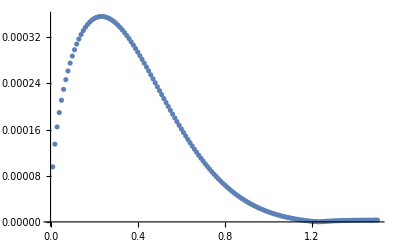

```mathematica
ListPlot[intV]
```

```mathematica
intVInter=Interpolation[Re[intV]];
```

```mathematica
rad0=Limit[Rinf[kk α μ,0,r]/.{ a0-> 1/(μ α)},r->0]
```

2 ⅇ^(π/(2 kk)) kk α μ Abs[Gamma[1-ⅈ/kk]]

```mathematica
(*alpha terms [factored out of radial integral, jacobian r, jacobian k, k2 term, rad0 term]]*)
```

```mathematica
val2= FullSimplify[SphericalHarmonicY[0,0,θ,ϕ] 1/μ^(3/2)(α μ)^(7/2)  (1/(α μ))^3 (α μ)α μ NIntegrate[intVInter[kk] rad0/(α μ),{kk,0.01,1.5}],α>0&&μ>0&&r∈Reals]
```

0.000159484 α^(5/2) μ

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val+val2)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.44086×10^-7 λ^2 μ α^7+O[α]^(19/2)

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.67451×10^-9 λ^2 μ α^7+O[α]^10

## 211 x 422 → 433 x BH (200)

```mathematica
(*Quit[]*)
```

```mathematica
(*411 x 411 -> 422 x BH*)
```

```mathematica
10^-12(1-α^2/(2 n^2))/.{μ-> 10^-12, α->0.1047783,n->2}
```

9.98628×10^-13

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
ωnew =  ωerg[2,α,μ]+ωerg[4,α,μ]-ωerg[4,α,μ];
kDiff =FullSimplify[(μ^2-ωerg[2,α,μ]^2)-( μ^2- ωnew^2)]
```

0

```mathematica
k2=Normal[Series[kDiff,{α,0,4}]]
```

0

```mathematica
ωnew =  ωerg[2,α,μ]+ωerg[4,α,μ]-ωerg[4,α,μ]//FullSimplify
```

μ-(α^2 μ)/8

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,4}]]]
```

(α^2 μ^2)/4-(α^4 μ^2)/64

```mathematica
ωerg2[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^4(2l-3n + 1)/(l+1/2));
```

```mathematica
k21
```

0

(277 α^4 μ^2)/280

```mathematica
NumberForm[ωnew/μ,10]/.{μ-> 3 10^-13,α-> 0.0314335106}
```

0.9998763569

```mathematica
NumberForm[ωerg2[2,α,μ,0]/μ,10]/.{μ-> 3 10^-13,α-> 0.0314335106}
```

0.999875874

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
```

1/(2 √π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
kDiff =FullSimplify[(μ^2-ωerg2[1,α,μ,0]^2)-( μ^2- ωnew^2)] ;
k21=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]]
```

(3 α^2 μ^2)/4+(2167 α^4 μ^2)/280

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[3,-3,θ,ϕ](-1)^3 SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[2,2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

3/(4 √7 π)

```mathematica
val=0;
(Do[hold=1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[4,2,r/(α μ)]Rb[4,3,r/(α μ)]/.{a0-> 1/(μ α)};

ωnew =  ωerg2[2,α,μ,1]+ωerg2[4,α,μ,2]-ωerg2[4,α,μ,3];
kDiff =FullSimplify[(μ^2-ωerg2[n,α,μ,0]^2)-( μ^2- ωnew^2)] ;
k21=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k21== 0/.{α->1,μ->1} , kuse=k2,kuse=k21];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,10}]);
FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,4}],α>0&&μ>0]
```

7.82881×10^-11 λ^2 μ α^3+O[α]^(9/2)

1.88108×10^-12 λ^2 μ α^3+O[α]^8

```mathematica
1.1 10^-9 λ^2 μ α^3/.{λ->1, μ->1 10^-12,α->0.10477836899}
```

1.26534×10^-24

```mathematica
6.229965308065563*^-12 λ^2 μ α^3/.{λ->1, μ-> 3 10^-13,α->0.0314335}
```

5.80477×10^-29

## 211 x 311 → 322 x BH [damps grow heavily...]

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
FullSimplify[SphericalHarmonicY[2,-2,θ,ϕ](-1)^2 SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]]
```

(3 √(15/2) Sin[θ]^4)/(32 π^(3/2))

```mathematica
ωnew =  ωerg[2,α,μ]+ωerg[3,α,μ]-ωerg[3,α,μ]//FullSimplify
```

μ-(α^2 μ)/8

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,4}]]]
```

(α^2 μ^2)/4-(α^4 μ^2)/64

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
```

1/(2 √π)

```mathematica
(*Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];*)
```

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ](-1)^2 SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[3,1,r/(α μ)] Rb[2,1,r/(α μ)]Rb[3,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
 Abs[SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15])/.{a0-> 1/(μ α)}];
,{n,2,2}]);
```

```mathematica
Series[ FullSimplify[ 1/μ 4 α^2 λ^2 val^2,α>0&&μ>0&&α<1],{α,0,3}]
```

2.24401×10^-8 λ^2 μ α^3+O[α]^4

```mathematica
(*k > 0 part*)
```

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,4}]]]
```

(α^2 μ^2)/4-(α^4 μ^2)/64

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[3,1,r/(α μ)]Rb[3,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
Abs[ SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)}];
,{n,2,2}]);
```

```mathematica
intTerm= FullSimplify[1/(2π)1/(k2+(kk α μ)^2)1/2 1/(2μ)^(3/2)RinfC[kk α μ ,0,r]Rb[2,1,r] Rb[3,1,r]Rb[3,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)} ,α>0&&μ>0]
```

(32 ⅇ^(π/(2 kk)-(7 r)/6+ⅈ kk r) kk (-6+r) r^4 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(19683 √15 π (-16-64 kk^2+α^2))

```mathematica
test = Normal[Series[intTerm,{α,0,4}]]
```

(32 ⅇ^(π/(2 kk)-(7 r)/6+ⅈ kk r) kk (-6+r) r^4 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(19683 √15 (-16-64 kk^2) π)

```mathematica
intV=Table[{kk,Abs[NIntegrate[1/(α^(7/2) μ^2)test r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6]]},{kk,0.01,1.5,.005}];
```

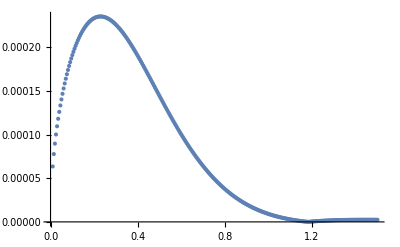

```mathematica
ListPlot[intV]
```

```mathematica
intVInter=Interpolation[Re[intV]];
```

```mathematica
rad0=Limit[Rinf[kk α μ,0,r]/.{ a0-> 1/(μ α)},r->0]
```

2 ⅇ^(π/(2 kk)) kk α μ Abs[Gamma[1-ⅈ/kk]]

```mathematica
(*alpha terms [factored out of radial integral, jacobian r, jacobian k, k2 term, rad0 term]]*)
```

```mathematica
val2= FullSimplify[SphericalHarmonicY[0,0,θ,ϕ] 1/μ^(3/2)(α μ)^(7/2)  (1/(α μ))^3 (α μ)α μ NIntegrate[intVInter[kk] rad0/(α μ),{kk,0.001,1.5}],α>0&&μ>0&&r∈Reals]
```

0.000101585 α^(5/2) μ

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val+val2)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.24401×10^-8 λ^2 μ α^3+6.08697×10^-8 λ^2 μ α^5+4.12779×10^-8 λ^2 μ α^7+O[α]^(19/2)

## 411 x 311 → 322 x BH [?]

```mathematica
ωerg2[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^4(2l-3n + 1)/(l+1/2));
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
n1=4;n2=n3=3;
l1=m1=1;l2=m2=1;l3=m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
(Do[hold=1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};

ωnew =  ωerg2[n1,α,μ,l1]+ωerg2[n2,α,μ,l2]-ωerg2[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2-ωerg2[n,α,μ,0]^2)-( μ^2- ωnew^2)] ;
k21=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k21== 0/.{α->1,μ->1} , kuse=k2,kuse=k21];

val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,10}]);
FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,4}],α>0&&μ>0]
```

1.85756×10^-10 λ^2 μ α^3+O[α]^(9/2)

```mathematica
(*k > 0 part*)
```

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,4}]]]
```

(α^2 μ^2)/4-(α^4 μ^2)/64

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[3,1,r/(α μ)]Rb[3,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
Abs[ SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)}];
,{n,2,2}]);
```

```mathematica
intTerm= FullSimplify[1/(2π)1/(k2+(kk α μ)^2)1/2 1/(2μ)^(3/2)RinfC[kk α μ ,0,r]Rb[2,1,r] Rb[3,1,r]Rb[3,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)} ,α>0&&μ>0]
```

(32 ⅇ^(π/(2 kk)-(7 r)/6+ⅈ kk r) kk (-6+r) r^4 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(19683 √15 π (-16-64 kk^2+α^2))

```mathematica
test = Normal[Series[intTerm,{α,0,4}]]
```

(32 ⅇ^(π/(2 kk)-(7 r)/6+ⅈ kk r) kk (-6+r) r^4 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(19683 √15 (-16-64 kk^2) π)

```mathematica
intV=Table[{kk,Abs[NIntegrate[1/(α^(7/2) μ^2)test r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6]]},{kk,0.01,1.5,.005}];
```

```mathematica
ListPlot[intV]
```

-Graphics-

```mathematica
intVInter=Interpolation[Re[intV]];
```

```mathematica
rad0=Limit[Rinf[kk α μ,0,r]/.{ a0-> 1/(μ α)},r->0]
```

2 ⅇ^(π/(2 kk)) kk α μ Abs[Gamma[1-ⅈ/kk]]

```mathematica
(*alpha terms [factored out of radial integral, jacobian r, jacobian k, k2 term, rad0 term]]*)
```

```mathematica
val2= FullSimplify[SphericalHarmonicY[0,0,θ,ϕ] 1/μ^(3/2)(α μ)^(7/2)  (1/(α μ))^3 (α μ)α μ NIntegrate[intVInter[kk] rad0/(α μ),{kk,0.001,1.5}],α>0&&μ>0&&r∈Reals]
```

0.000101585 α^(5/2) μ

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val+val2)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.24401×10^-8 λ^2 μ α^3+6.08697×10^-8 λ^2 μ α^5+4.12779×10^-8 λ^2 μ α^7+O[α]^(19/2)

## 411 x 311 → 322 x BH [?]

```mathematica
ωerg2[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^4(2l-3n + 1)/(l+1/2));
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
n1=4;n2=4;n3=3;
l1=m1=1;l2=m2=1;l3=m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
(Do[hold=1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};

ωnew =  ωerg2[n1,α,μ,l1]+ωerg2[n2,α,μ,l2]-ωerg2[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2-ωerg2[n,α,μ,0]^2)-( μ^2- ωnew^2)] ;
k21=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k21== 0/.{α->1,μ->1} , kuse=k2,kuse=k21];

val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,70}]);
FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.30312×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
k2 = Normal[FullSimplify[Series[μ^2- ωnew^2,{α,0,4}]]]
```

(α^2 μ^2)/4-(α^4 μ^2)/64

```mathematica
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

(√(3/10))/(2 π)

```mathematica
val=0;
(Do[hold=1/2 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[3,1,r/(α μ)]Rb[3,2,r/(α μ)]/.{a0-> 1/(μ α)};
val+=
Abs[ SphericalHarmonicY[0,0,θ,ϕ]Limit[Rb[n,0,r],r->0](CG/(k2-((α^2 μ^2)/n^2))α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity}])/.{a0-> 1/(μ α)}];
,{n,2,2}]);
```

```mathematica
intTerm= FullSimplify[1/(2π)1/(k2+(kk α μ)^2)1/2 1/(2μ)^(3/2)RinfC[kk α μ ,0,r]Rb[2,1,r] Rb[3,1,r]Rb[3,2,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)} ,α>0&&μ>0]
```

(32 ⅇ^(π/(2 kk)-(7 r)/6+ⅈ kk r) kk (-6+r) r^4 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(19683 √15 π (-16-64 kk^2+α^2))

```mathematica
test = Normal[Series[intTerm,{α,0,4}]]
```

(32 ⅇ^(π/(2 kk)-(7 r)/6+ⅈ kk r) kk (-6+r) r^4 α^(7/2) μ^2 Abs[Gamma[(ⅈ+kk)/kk]] Hypergeometric1F1[(-ⅈ+kk)/kk,2,-2 ⅈ kk r])/(19683 √15 (-16-64 kk^2) π)

```mathematica
intV=Table[{kk,Abs[NIntegrate[1/(α^(7/2) μ^2)test r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6]]},{kk,0.01,1.5,.005}];
```

```mathematica
ListPlot[intV]
```

-Graphics-

```mathematica
intVInter=Interpolation[Re[intV]];
```

```mathematica
rad0=Limit[Rinf[kk α μ,0,r]/.{ a0-> 1/(μ α)},r->0]
```

2 ⅇ^(π/(2 kk)) kk α μ Abs[Gamma[1-ⅈ/kk]]

```mathematica
(*alpha terms [factored out of radial integral, jacobian r, jacobian k, k2 term, rad0 term]]*)
```

```mathematica
val2= FullSimplify[SphericalHarmonicY[0,0,θ,ϕ] 1/μ^(3/2)(α μ)^(7/2)  (1/(α μ))^3 (α μ)α μ NIntegrate[intVInter[kk] rad0/(α μ),{kk,0.001,1.5}],α>0&&μ>0&&r∈Reals]
```

0.000101585 α^(5/2) μ

```mathematica
FullSimplify[Series[ 1/μ 4 α^2 λ^2 (val+val2)^2/.{a0->(μ α)^-1},{α,0,9}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.24401×10^-8 λ^2 μ α^3+6.08697×10^-8 λ^2 μ α^5+4.12779×10^-8 λ^2 μ α^7+O[α]^(19/2)

## Z x Y → 321 x Inf [NOT POSSIBLE ENERGICS]

```mathematica
(*411 x 422 -> 211 x Inf*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
Series[ωerg[4,α,μ]+ωerg[4,α,μ]-ωerg[3,α,μ],{α,0,2}]-μ
```

-(μ α^2)/144+O[α]^3

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c) ;
```

```mathematica
Coefficient[Expand[ϕ1^3], ⅇ^(-2 ⅈ t ω3-ⅈ t ω2)]
```

3 α2 α3^2 ψ2 ψ3^2

```mathematica
FullSimplify[SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]]
```

(3 √(15/2) ⅇ^(2 ⅈ ϕ) Sin[θ]^4)/(32 π^(3/2))

```mathematica
CG = Block[{l=2,m=-2},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

9/(28 π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
ωnew =  ωerg[4,α,μ]+ωerg[4,α,μ]-ωerg[2,α,μ]//FullSimplify
```

μ+(α^2 μ)/16

```mathematica
k=Normal[FullSimplify[Series[√(ωnew^2-μ^2),{α,0,2}],μ>0&&α>0]]
```

(α μ)/(2 √2)

```mathematica
FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]
```

(r^2 (r/(α μ))'[x])/(α^2 μ^2)

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Conjugate[Rinf[k,2,r ]]Rb[4,2,r] Rb[4,1,r]Rb[2,1,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

-(ⅇ^(√2 π+1/4 ⅈ (4 ⅈ+√2) r) (-12+r) r^6 (80+(-20+r) r) α^(11/2) μ^4 Abs[Gamma[3-2 ⅈ √2]] Conjugate[Hypergeometric1F1[3+2 ⅈ √2,6,(ⅈ r)/(√2)]])/(11324620800 √2)

```mathematica
ff=FullSimplify[(CG (4π)(-I)^l)/(2 k)α^(11/2) μ^4(1/(α μ))^3 NIntegrate[-(ⅇ^(√2 π+1/4 ⅈ (4 ⅈ+√2) r) (-12+r) r^6 (80+(-20+r) r)  Abs[Gamma[3-2 ⅈ √2]] Hypergeometric1F1[3-2 ⅈ √2,6,(-ⅈ r)/(√2)])/(11324620800 √2),{r,0,Infinity}]/.{l->3},α>0&&μ>0&&r∈Reals]
```

(4.84386×10^-13+0.0000343329 ⅈ) α^(3/2)

```mathematica
Series[ωnew k,{α,0,1}]
```

(μ^2 α)/(2 √2)+O[α]^2

```mathematica
FullSimplify[Series[ 2 ((μ^2 α)/(2 √2))/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.27819×10^-12 λ^2 μ^2 α^4+O[α]^6

```mathematica
5.278193048805911*^-12 λ^2 μ^2 α^4/.{λ-> (μ/fa)^2}
```

(5.27819×10^-12 α^4 μ^6)/fa^4

## Z x Y → 421 x Inf [NOT POSSIBLE ENERGICS]

```mathematica
(*411 x 422 -> 211 x Inf*)
```

```mathematica
ωerg[n_,α_,μ_]:=μ (1-α^2/(2 n^2));
```

```mathematica
Series[ωerg[4,α,μ]+ωerg[4,α,μ]-ωerg[3,α,μ],{α,0,2}]-μ
```

-(μ α^2)/144+O[α]^3

```mathematica
dΩ = Sin[θ];
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c) ;
```

```mathematica
Coefficient[Expand[ϕ1^3], ⅇ^(-2 ⅈ t ω3-ⅈ t ω2)]
```

3 α2 α3^2 ψ2 ψ3^2

```mathematica
FullSimplify[SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]]
```

(3 √(15/2) ⅇ^(2 ⅈ ϕ) Sin[θ]^4)/(32 π^(3/2))

```mathematica
CG = Block[{l=2,m=-2},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[1,-1,θ,ϕ](-1)SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[1,1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

9/(28 π)

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
ωnew =  ωerg[4,α,μ]+ωerg[4,α,μ]-ωerg[2,α,μ]//FullSimplify
```

μ+(α^2 μ)/16

```mathematica
k=Normal[FullSimplify[Series[√(ωnew^2-μ^2),{α,0,2}],μ>0&&α>0]]
```

(α μ)/(2 √2)

```mathematica
FullSimplify[r^2 D[r[x],x]/.{r->r/(α μ)}]
```

(r^2 (r/(α μ))'[x])/(α^2 μ^2)

```mathematica
FullSimplify[1/2 1/(2μ)^(3/2)Conjugate[Rinf[k,2,r ]]Rb[4,2,r] Rb[4,1,r]Rb[2,1,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0]
```

-(ⅇ^(√2 π+1/4 ⅈ (4 ⅈ+√2) r) (-12+r) r^6 (80+(-20+r) r) α^(11/2) μ^4 Abs[Gamma[3-2 ⅈ √2]] Conjugate[Hypergeometric1F1[3+2 ⅈ √2,6,(ⅈ r)/(√2)]])/(11324620800 √2)

```mathematica
ff=FullSimplify[(CG (4π)(-I)^l)/(2 k)α^(11/2) μ^4(1/(α μ))^3 NIntegrate[-(ⅇ^(√2 π+1/4 ⅈ (4 ⅈ+√2) r) (-12+r) r^6 (80+(-20+r) r)  Abs[Gamma[3-2 ⅈ √2]] Hypergeometric1F1[3-2 ⅈ √2,6,(-ⅈ r)/(√2)])/(11324620800 √2),{r,0,Infinity}]/.{l->3},α>0&&μ>0&&r∈Reals]
```

(4.84386×10^-13+0.0000343329 ⅈ) α^(3/2)

```mathematica
Series[ωnew k,{α,0,1}]
```

(μ^2 α)/(2 √2)+O[α]^2

```mathematica
FullSimplify[Series[ 2 ((μ^2 α)/(2 √2))/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.27819×10^-12 λ^2 μ^2 α^4+O[α]^6

```mathematica
5.278193048805911*^-12 λ^2 μ^2 α^4/.{λ-> (μ/fa)^2}
```

(5.27819×10^-12 α^4 μ^6)/fa^4

## Check

```mathematica
Block[{n=3,l=2,m=2},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l,-m,θ,ϕ](-1)^m Rb[n,l,r]^2 r^2 Sin[θ],{r,0,Infinity},{θ,0,π},{ϕ,0,2π}]]
```

ConditionalExpression[1, Re[a0]>0]

## Need to think about

```mathematica
[311 (damped resonance),321 (cant be pumped, growth rate suppressed by many orders magntiude),421 (cant be pumped, growth rate suppressed by many orders magntiude),431 (tiny growth rate, cant be pumped), 432]
```

can 321, 421 grow? Can 432 grow? clear 311 fully damped. 
- 321 can only grow if m=1 spin down does not occur, but this occurs on long timescales. same with 421 and 431 [neither can be pumped with  BH final state! or with infinity from kinematics]?
-432 can only grow if 322 does not exact spin, but grows on very long timescale.... [can be pumped via 211 x 321, but 321 cannot grow? can anything elsee pump??]

Hmm lets see
n21 x n’11  -> 432 x BH, but this cant happen because it would require n21 state! GOOD!

## Freq shifts

### random

```mathematica
ϕ=√(N211/(2μ))Exp[-I ω2 t]ψ211 +√(N322/(2μ))Exp[-I ω3 t]ψ322 +√(N411/(2μ))Exp[-I ω4 t]ψ411
```

(ⅇ^(-ⅈ t ω2) √(N211/μ) ψ211)/(√2)+(ⅇ^(-ⅈ t ω3) √(N322/μ) ψ322)/(√2)+(ⅇ^(-ⅈ t ω4) √(N411/μ) ψ411)/(√2)

```mathematica
fullP=Expand[FullSimplify[Expand[1/6(ϕ)^2 Conjugate[ϕ]],N211>0&&N322>0&&N411>0&&ω2>0&&ω3>0&&ω4>0&&t>0&&μ>0]]
```

(ⅇ^(ⅈ t ω2+2 ⅈ t (ω3+ω4)-2 ⅈ t (ω2+ω3+ω4)) N211 √(N211/μ) ψ211^2 Conjugate[ψ211])/(12 √2 μ)+(ⅇ^(ⅈ t ω2-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+ω3+2 ω4)) √(N211 N322) √(N211/μ) ψ211 ψ322 Conjugate[ψ211])/(6 √2 μ)+(ⅇ^(ⅈ t ω2+2 ⅈ t (ω2+ω4)-2 ⅈ t (ω2+ω3+ω4)) N322 √(N211/μ) ψ322^2 Conjugate[ψ211])/(12 √2 μ)+(ⅇ^(ⅈ t ω2-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+2 ω3+ω4)) √(N211 N411) √(N211/μ) ψ211 ψ411 Conjugate[ψ211])/(6 √2 μ)+(ⅇ^(ⅈ t ω2-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (2 ω2+ω3+ω4)) √(N322 N411) √(N211/μ) ψ322 ψ411 Conjugate[ψ211])/(6 √2 μ)+(ⅇ^(ⅈ t ω2+2 ⅈ t (ω2+ω3)-2 ⅈ t (ω2+ω3+ω4)) N411 √(N211/μ) ψ411^2 Conjugate[ψ211])/(12 √2 μ)+(ⅇ^(ⅈ t ω3+2 ⅈ t (ω3+ω4)-2 ⅈ t (ω2+ω3+ω4)) N211 √(N322/μ) ψ211^2 Conjugate[ψ322])/(12 √2 μ)+(ⅇ^(ⅈ t ω3-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+ω3+2 ω4)) √(N211 N322) √(N322/μ) ψ211 ψ322 Conjugate[ψ322])/(6 √2 μ)+(ⅇ^(ⅈ t ω3+2 ⅈ t (ω2+ω4)-2 ⅈ t (ω2+ω3+ω4)) N322 √(N322/μ) ψ322^2 Conjugate[ψ322])/(12 √2 μ)+(ⅇ^(ⅈ t ω3-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+2 ω3+ω4)) √(N211 N411) √(N322/μ) ψ211 ψ411 Conjugate[ψ322])/(6 √2 μ)+(ⅇ^(ⅈ t ω3-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (2 ω2+ω3+ω4)) √(N322 N411) √(N322/μ) ψ322 ψ411 Conjugate[ψ322])/(6 √2 μ)+(ⅇ^(ⅈ t ω3+2 ⅈ t (ω2+ω3)-2 ⅈ t (ω2+ω3+ω4)) N411 √(N322/μ) ψ411^2 Conjugate[ψ322])/(12 √2 μ)+(ⅇ^(ⅈ t ω4+2 ⅈ t (ω3+ω4)-2 ⅈ t (ω2+ω3+ω4)) N211 √(N411/μ) ψ211^2 Conjugate[ψ411])/(12 √2 μ)+(ⅇ^(ⅈ t ω4-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+ω3+2 ω4)) √(N211 N322) √(N411/μ) ψ211 ψ322 Conjugate[ψ411])/(6 √2 μ)+(ⅇ^(ⅈ t ω4+2 ⅈ t (ω2+ω4)-2 ⅈ t (ω2+ω3+ω4)) N322 √(N411/μ) ψ322^2 Conjugate[ψ411])/(12 √2 μ)+(ⅇ^(ⅈ t ω4-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+2 ω3+ω4)) √(N211 N411) √(N411/μ) ψ211 ψ411 Conjugate[ψ411])/(6 √2 μ)+(ⅇ^(ⅈ t ω4-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (2 ω2+ω3+ω4)) √(N322 N411) √(N411/μ) ψ322 ψ411 Conjugate[ψ411])/(6 √2 μ)+(ⅇ^(2 ⅈ t (ω2+ω3)+ⅈ t ω4-2 ⅈ t (ω2+ω3+ω4)) N411 √(N411/μ) ψ411^2 Conjugate[ψ411])/(12 √2 μ)

```mathematica
FullSimplify[(ⅇ^(ⅈ t ω2-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+ω3+2 ω4)) √(N211 N322) √(N211/μ) ψ211 ψ322 Conjugate[ψ211])/(6 √2 μ)]
```

(ⅇ^(-ⅈ t ω3) √(N211 N322) √(N211/μ) ψ211 ψ322 Conjugate[ψ211])/(6 √2 μ)

```mathematica
FullSimplify[(ⅇ^(ⅈ t ω2+2 ⅈ t (ω3+ω4)-2 ⅈ t (ω2+ω3+ω4)) N211 √(N211/μ) ψ211^2 Conjugate[ψ211])/(12 √2 μ)]
```

(ⅇ^(-ⅈ t ω2) (N211/μ)^(3/2) ψ211 Abs[ψ211]^2)/(12 √2)

```mathematica
FullSimplify[(ⅇ^(ⅈ t ω4-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+2 ω3+ω4)) √(N211 N411) √(N411/μ) ψ211 ψ411 Conjugate[ψ411])/(6 √2 μ)]
```

(ⅇ^(-ⅈ t ω2) √(N211 N411) √(N411/μ) ψ211 ψ411 Conjugate[ψ411])/(6 √2 μ)

```mathematica
FullSimplify[(ⅇ^(ⅈ t ω2-2 ⅈ t (ω2+ω3+ω4)+ⅈ t (ω2+2 ω3+ω4)) √(N211 N411) √(N211/μ) ψ211 ψ411 Conjugate[ψ211])/(6 √2 μ)]
```

(ⅇ^(-ⅈ t ω4) √(N211 N411) √(N211/μ) ψ211 ψ411 Conjugate[ψ211])/(6 √2 μ)

### ex

```mathematica
CG = Block[{l=1,m=1},Integrate[Conjugate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l,m,θ,ϕ]] SphericalHarmonicY[l,m,θ,ϕ]^2 Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

3/(10 π)

```mathematica
NIntegrate[1/(4 μ^2)1/2 CG Rb[2,1,r]^4 r^2/.{a0-> 1/(α μ)}/.{μ-> 3 10^-13, α-> 0.031433},{r,0,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {5.28157×10^14}. NIntegrate obtained 1.08214×10^-21 and 3.43247×10^-22 for the integral and error estimates.

1.08214×10^-21

```mathematica
ωerg2[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^4(2l-3n + 1)/(l+1/2));
```

```mathematica
ωnew =  ωerg2[2,α,μ,1](1+ϵ)+ωerg2[4,α,μ,2]-ωerg2[4,α,μ,3];
kDiff =FullSimplify[(μ^2-ωerg2[2,α,μ,0]^2)-( μ^2- ωnew^2)]
```

-(-1+α^2/8+(81 α^4)/128)^2 μ^2+((-4480 (1+ϵ)+560 α^2 (1+ϵ)+α^4 (619+595 ϵ))^2 μ^2)/20070400

```mathematica
k2=Normal[Series[kDiff,{α,0,4},{ϵ,0,1}]]
```

2 ϵ μ^2-1/2 α^2 ϵ μ^2+α^4 ((277 μ^2)/280-(143 ϵ μ^2)/280)

```mathematica
k2/.{ϵ->0}
```

(277 α^4 μ^2)/280

```mathematica
test=Solve[2(α^5(Mp/f)^2 10^-4 ϵ211)==(277 α^4)/280,ϵ211]
```

{{ϵ211→(34625 f^2)/(7 Mp^2 α)}}

```mathematica
test/.{f-> 10^14,Mp-> 10^19,α-> 0.2}
```

{{ϵ211→2.47321×10^-6}}

```mathematica
ωnew =  ωerg2[2,α,μ,1]+ωerg2[4,α,μ,2](1+ϵ)-ωerg2[4,α,μ,3];
kDiff =FullSimplify[(μ^2-ωerg2[2,α,μ,0]^2)-( μ^2- ωnew^2)]
```

-(-1+α^2/8+(81 α^4)/128)^2 μ^2+((-71680 (1+ϵ)+2240 α^2 (4+ϵ)+α^4 (9904+819 ϵ))^2 μ^2)/5138022400

```mathematica
k2=Normal[Series[kDiff,{α,0,4},{ϵ,0,1}]]
```

2 ϵ μ^2-5/16 α^2 ϵ μ^2+α^4 ((277 μ^2)/280-(10443 ϵ μ^2)/35840)

```mathematica
k2/.{ϵ->0}
```

(277 α^4 μ^2)/280

```mathematica
test=Solve[2(α^5(Mp/f)^2 10^-4 ϵ211)==(277 α^4)/280,ϵ211]
```

{{ϵ211→(34625 f^2)/(7 Mp^2 α)}}

```mathematica
test/.{f-> 10^14,Mp-> 10^19,α-> 0.2}
```